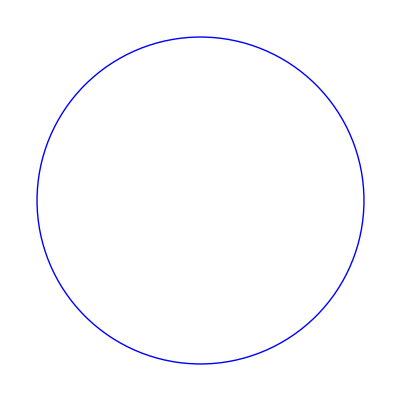

-Graphics-

-Graphics-

-Graphics-

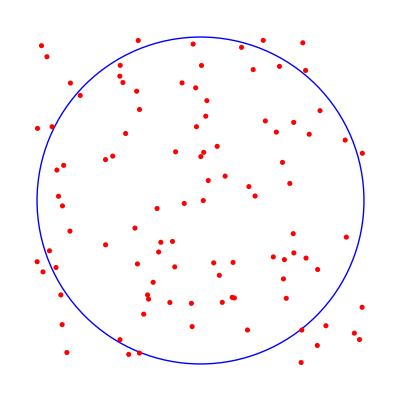

```mathematica
p1=Graphics[{Blue,Thick,Circle[{0.5,0.5},0.5]}]
p2=Graphics[{Blue,Thick,Circle[]},GridLines->{Range[-1,1,0.1],Range[-1,1,0.1]}]
p3=Graphics[{EdgeForm[Directive[Thick,Blue]],Opacity[0.0],Pink,Rectangle[]}]
Show[p1,p3]
(*Generate lots of random points, plot them and add them to figure*)
num=100;
xrand=RandomReal[1,num];
yrand=RandomReal[1,num];
p4=ListPlot[Transpose[{xrand,yrand}],PlotStyle->Red,Frame->False];
Show[p1,p3,p4]
```

```mathematica
Graphics[{Blue,Thick,Circle[]},GridLines->{Range[-1,1,0.1],Range[-1,1,0.1]},GridLineStyle->Directive[Thick]]
```

-Graphics-

```mathematica
Range[-1,1,0.1]
```

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}